## Information and copyright

Simulation code associated with “Social distancing strategies for curbing the COVID-19 epidemic”, 
by S.M. Kissler, C. Tedijanto, M. Lipsitch, and Y.H. Grad.
Correspondence: skissler@hsph.harvard.edu, ygrad@hsph.harvard.edu

Last modified: 22 March 2020

    This program is free software: you can redistribute it and/or modify
    it under the terms of the GNU General Public License as published by
    the Free Software Foundation, either version 3 of the License, or
    (at your option) any later version.

    This program is distributed in the hope that it will be useful,
    but WITHOUT ANY WARRANTY; without even the implied warranty of
    MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
    GNU General Public License for more details.

    You should have received a copy of the GNU General Public License
    along with this program.  If not, see <https://www.gnu.org/licenses/>.

## Set parameter values and define functions:

```mathematica
(*Seasonal forcing*)
beta[t_,amplitude_,baseline_,phival_,gammaval_]:=gammaval*(amplitude/2*Cos[2*Pi*(t-phival)/52]+(amplitude/2+baseline))

pC = (0.3)*(0.044); (*Probability of needing critical care*)
pH = (0.7)*(0.044); (*Probability of hospitalization but not critical care*)
pS = 1-(pC + pH); (*Probability of not needing care*)

nuval = 1/(4.6/7); (*Rate of progressing to infectiousness, weeks*)
gammaval = 1/(5/7); (*Rate of losing infectiousness or going to the hospital, weeks*)

deltaHval = 1/(8/7); (*Rate of leaving hospital for those not going to critical care, weeks*)
deltaCval = 1/(6/7); (*Rate of leaving hospital and going to critical care, weeks*)
xiCval = 1/(10/7); (*Rate of leaving critical care, weeks*)
 
amplitude = 0.6; (*Amplitude of R0*)
baseline = 1.4; (*Baseline R0 value*)
phival= -3.8; (*Seasonality shift, weeks*)

kappaval = 0.01; (*Increase in force of infection for establishment*)
importtime = (31+29+11)/7;  (*Establishment time*)
importlength = 0.5; (*Duration of pulse in force of infection for establishment, weeks*)

tmax = 5*52; (*Max time to run the simulation, weeks*)

plotwindow = {0, 64}; (*Length of window for plotting, weeks*)
plotwindowlong = {0, 52*2.5}; (*Longer plot window, weeks*)
fs = 18; (*Font size for plots*)
```

```mathematica
thresholdprevon = 0.00375; (*For intermittent strategies, prevalence threshold to turn on distancing*)
thresholdprevoff = 0.001; (*For intermittent strategies, prevalence threshold to turn off distancing*)

CCthreshold = .000089; (*Critical care threshold (Li et al, "he Demand for Inpatient and ICU Beds for COVID-19 in the US" 2020)*)
```

```mathematica
(*Tick marks for plotting dates*)
dateticks = {
{0, Rotate["Jan",π/2]},
{0, Text[Style["\n\n2020", FontSize->14]]},
{(31)/7,""},
{(31+28)/7,""},
{(31+28+31)/7, Rotate["Apr",π/2]}, 
{(31+28+31+30)/7,""}, 
{(31+28+31+30+31)/7,""}, 
{(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{(31+28+31+30+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31)/7, ""},
{(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]},
{(31+28+31+30+31+30+31+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31+30+31+30)/7, ""},
{52, Rotate["Jan",π/2]},
{52, Text[Style["\n\n2021", FontSize->14]]},
{52+(31)/7,""}, 
{52+(31+28)/7, ""}, 
{52+(31+28+31)/7, Rotate["Apr",π/2]}, 
{52+(31+28+31+30)/7, ""}, 
{52+(31+28+31+30+31)/7, ""}, 
{52+(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{52+(31+28+31+30+31+30+31)/7, ""},
{52+(31+28+31+30+31+30+31+31)/7, ""},
{52+(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]},
{52+(31+28+31+30+31+30+31+31+30+31)/7,""},
{52+(31+28+31+30+31+30+31+31+30+31+30)/7,""},
{52*2, Rotate["Jan",π/2]}, 
{52*2, Text[Style["\n\n2022", FontSize->14]]}, 
{52*2+(31)/7, ""}, 
{52*2+(31+28)/7, ""}, 
{52*2+(31+28+31)/7, Rotate["Apr",π/2]}, 
{52*2+(31+28+31+30)/7,""}, 
{52*2+(31+28+31+30+31)/7,""}, 
{52*2+(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{52*2+(31+28+31+30+31+30+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]}};
```

## Simulations with fixed-duration interventions:

```mathematica
npifactor = 0.2; (*Fractional decline in R0 due to social distancing (0 = no intervention, 1 = all contact ceases*)
npistart = importtime + 2; (*Start time of distancing, weeks*)
npiend = npistart + 4; (*End time of distancing, weeks *)
seasonality=1; (*Amount of seasonality (1 = full seasonality, 0 = no seasonality so that R0 is equal to wintertime R0)*)
solfixed=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

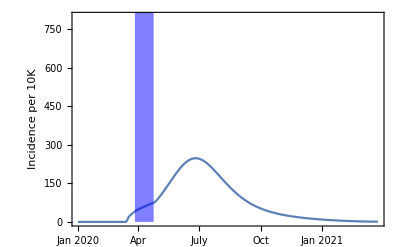

```mathematica
Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solfixed]
},Join[{t},plotwindow], PlotRange->{0,800}, FrameTicks->{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}},Automatic}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Incidence per 10K"},
Epilog->{Blue,Opacity[.5],Rectangle[{npistart,0},{npiend,1000000}]}]
```

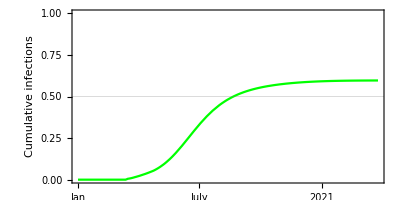

```mathematica
Plot[{
Evaluate[1-Sq[t]/.solfixed]
},Join[{t},plotwindow], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{dateticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, PlotStyle->Green, AspectRatio->0.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

## Simulations with intermittent interventions:

```mathematica
npifactor = 0.6; (*Fractional decline in R0 due to social distancing (0 = no intervention, 1 = all contact ceases*)
seasonality=1;(*Amount of seasonality (1 = full seasonality, 0 = no seasonality so that R0 is equal to wintertime R0)*)
solint=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

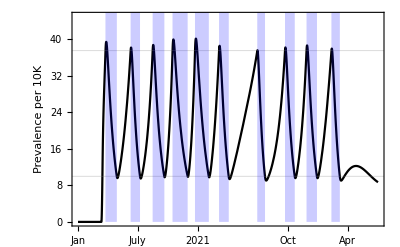

```mathematica
Show[Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solint]
},Join[{t},plotwindowlong], PlotRange->All, FrameTicks->{dateticks,Automatic}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K"}, PlotStyle->Black, GridLines->{{},{{10000*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*thresholdprevoff,{Black, Dashed, Opacity[1]}}}}],
Plot[10000*Evaluate[1-npi[t]/.solint],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}],
PlotRange->{0,45}
]
```

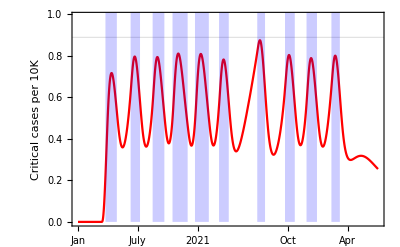

```mathematica
Show[
Plot[{
10000*Evaluate[CCq[t]/.solint]
},Join[{t},plotwindowlong], PlotRange->{0, 10000*CCthreshold+0.1}, FrameTicks->{dateticks,Automatic}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, PlotStyle->Red, FrameLabel->{None,"Critical cases per 10K"}, GridLines->{{},{10000*CCthreshold}}],
Plot[10000*Evaluate[1-npi[t]/.solint],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}],
PlotRange->{0, 10000*CCthreshold+0.1}
]
```

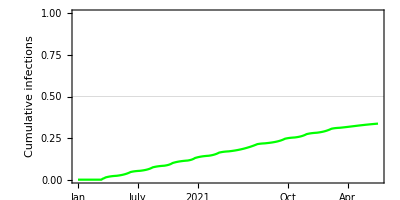

```mathematica
Plot[{
Evaluate[1-Sq[t]/.solint]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{dateticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, PlotStyle->Green, AspectRatio->0.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```